### Import Data

```mathematica
quarkData = <<"output/yukawa_quark.m";
Print["Number of Yu Yd 3x3 matrix pairs"]
Dimensions[quarkData]
```

Number of Yu Yd 3x3 matrix pairs

{1321,2,3,3}

```mathematica
{cMArray,cuData,cdData,ceData}=<<"output/cLcR04.m";
Dimensions/@{cuData,cdData,ceData}
```

{{1321,26,3,2},{1321,26,3,2},{1030,26,3,2}}

```mathematica
quarkAData  =<< "output/A_quark.m";
Dimensions[quarkAData]
```

{1321,4,3,3}

Check: 
	Quark data for Y, c and A have the same length

### Figures

Plotting parameters

```mathematica
colors=ColorData[97,"ColorList"];
```

Note Xu = - 2 cos^2 β, Xd = - 2 sin^2 β where tan β = 3

```mathematica
tanbeta = 3.; 
Xu = 2. 1^2 / (  1^2 + tanbeta^2 ); 
Xd = 2. tanbeta^2 / (  1^2 + tanbeta^2 );
```

#### F_ds for multiple σ0

Second index of AData (1, 2, 3, 4) stores (AuL, AuR, AdL, AdR)

```mathematica
data=cuData; Dimensions[data]
AData = quarkAData[[All,1;;2]]; Dimensions[AData]
```

{1321,26,3,2}

{1321,2,3,3}

```mathematica
σ0Array={1,2,3,4,5};
With[
{kMax = n, cmTotal =Dimensions[data][[2]],
Mpl = 1.22 10^19,Fa=1. 10^9,X=Xd,Δ=10,
α=0.5},
zIRArray = Mpl/Fa σ0Array/Sqrt[Δ-1];
outputSigma=Table[
Mpl /(X ( α AData[[k,2]].
DiagonalMatrix[ Table[ FermionAxionOverlap2[ data[[k, cmpt, whichQuark, 2]] ,Δ,σ0Array[[i]],zIRArray[[i]]],{whichQuark,3}] ].
ConjugateTranspose[ AData[[k,2]] ] - (* - for F_V, + for F_A *)
(1-α) AData[[k,1]].
DiagonalMatrix[ Table[ FermionAxionOverlap2[ data[[k, cmpt, whichQuark, 1]] ,Δ,σ0Array[[i]],zIRArray[[i]]],{whichQuark,3}] ].
ConjugateTranspose[ AData[[k,1]] ] ) ), (* Use AData[[, 4 and 3]] for down quark *)
{i,Range[Length[σ0Array]]},{k,kMax},{cmpt,cmTotal}]
];//AbsoluteTiming
```

{98.1606,Null}

```mathematica
y12vSigma =Table[Mean[Log10/@Abs[outputSigma[[σidx,All,cmpt,1,2]]]],{σidx,Length[σ0Array]},{cmpt,Dimensions[data][[2]]}];
```

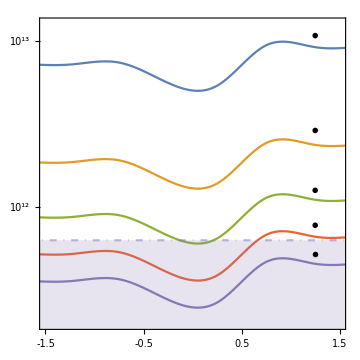

```mathematica
fig = Show[
ListPlot[
Table[{cMArray,#[[i]]}//Transpose,{i,Range[Length[σ0Array]]}],
PlotRange->{{-1.5,1.5},{11.3,13.1}},
FrameTicks->{{LogTicks,StripTickLabels[LogTicks]},{LinTicks,StripTickLabels[LinTicks]}},
FrameLabel->{MaTeX["c_M"],MaTeX["F^V_{sd}"]} (* Replace for F_V *)
]&@ y12vSigma,

(* Experimental limit *)
ListPlot[Table[{i,11.8},{i,cMArray}],PlotStyle->{DotDashed,Opacity[0.5],colors[[#]]},
Filling->Bottom,FillingStyle->Directive[Opacity[0.2],colors[[#]]]]& @ 5,

(* Labels for curve *)
Epilog->MapThread[Inset[#1,{#2,#3}]&,
{
Table[MaTeX["\sigma_0 = "~StringJoin~ToString[s]],{s,σ0Array}],
{1.25,1.25,1.25,1.25,1.25},
{12.99,12.42,12.06,11.85,11.68}+0.04
}
]
]
```

```mathematica
(* Export["Figures/sigma_constraint.pdf",fig] *)
```

Figures/sigma_constraint.pdf

#### F_ds for multiple Δ

```mathematica
ΔArray = {6, 9, 15,18};
With[
{kMax = n, cmTotal =Dimensions[data][[2]],
Mpl = 1.22 10^19,Fa=1. 10^9, σ0=3.,X=Xd,
α=0.5},
zIRArray = Mpl/Fa σ0/Sqrt[ΔArray-1];
outputDelta=Table[
Mpl /(X ( α AData[[k,2]].
DiagonalMatrix[ Table[ FermionAxionOverlap2[ data[[k, cmpt, whichQuark, 2]] ,ΔArray[[i]],σ0, zIRArray[[i]]],{whichQuark,3}] ].
ConjugateTranspose[ AData[[k,2]] ]-  (* - for F_V, + for F_A *)
(1-α) AData[[k,1]].
DiagonalMatrix[ Table[ FermionAxionOverlap2[ data[[k, cmpt, whichQuark, 1]] ,ΔArray[[i]],σ0, zIRArray[[i]]],{whichQuark,3}] ].
ConjugateTranspose[ AData[[k,1]] ] ) ),
{i,Range[Length[ΔArray]]},{k,kMax},{cmpt,cmTotal}]
];//Timing
```

{30.0781,Null}

```mathematica
y12vDelta =Table[Mean[Log10/@Abs[outputDelta[[Δidx,All,cmpt,1,2]]]],{Δidx,Range[Length[ΔArray]]},{cmpt,Dimensions[data][[2]]}];
```

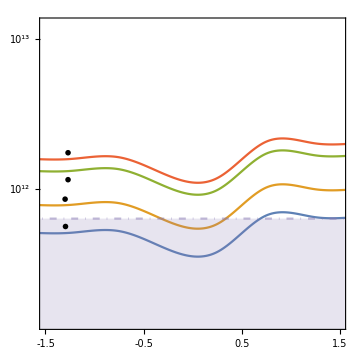

```mathematica
fig = Show[
ListPlot[
Table[{cMArray,#[[i]]}//Transpose,{i,Range[Length[ΔArray]]}],
PlotRange->{{-1.5,1.5},{11.1,13.1}},
FrameTicks->{{LogTicks,StripTickLabels[LogTicks]},{LinTicks,StripTickLabels[LinTicks]}},
FrameLabel->{MaTeX["c_M"],MaTeX["F^V_{sd}"]} (* Replace for F_V *)
]&@ y12vDelta,

(* Experimental limit *)
ListPlot[Table[{i,11.8},{i,cMArray}],PlotStyle->{DotDashed,Opacity[0.5],colors[[#]]},
Filling->Bottom,FillingStyle->Directive[Opacity[0.2],colors[[#]]]]& @ 5,

(* Labels for curve *)
Epilog->MapThread[Inset[#1,{#2,#3}]&,
{
Table[MaTeX["\Delta = "~StringJoin~ToString[s]],{s,ΔArray}],
{-1.3,-1.3,-1.27,-1.27},
{11.75,11.93,12.06,12.24}
}
]
]
```

```mathematica
(* Export["Figures/delta_constraint.pdf",fig] *)
```